In this analysis, we set everything in terms of the predator body size
Prey body size is then determined as a function of the predator body size: OptPreyMass = f[PredMass]

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqnP = (w*bPred*P*C +(1-w)* bPredSub*Sub*P) - μPred*P/.{bPred->bPred[Mp],bPredSub->bPredSub[Mp],μPred->μPred[Mp]}; (*,σPred->σPred[M],kC->kCons[M],Sub->Sub[M]*)
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+w*b*P)*C/.{k->kRes,λ->λ[Mp],μ->μ[Mp],σ->σ[Mp],b->b[Mp]};
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R)))*C/.{k->kRes,λ->λ[Mp],Y->Y[Mp]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC,0==eqnR},{P,C,R}]];
```

```mathematica
Psol = P/.LVSS[[5]]
Csol = C/.LVSS[[5]]
Rsol = R/.LVSS[[5]]
```

((8 λ[Mp])/w-(8 μ[Mp])/w+((-3 √kRes √w √α √bPred[Mp] √Y[Mp]+√(9 kRes w α bPred[Mp] Y[Mp]-16 λ[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp]))) (kRes w α bPred[Mp] Y[Mp]+2 (Sub (-1+w) bPredSub[Mp]+μPred[Mp]) σ[Mp]))/(√kRes w^(3/2) √α √bPred[Mp] √Y[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp])))/(8 b[Mp])

(Sub (-1+w) bPredSub[Mp]+μPred[Mp])/(w bPred[Mp])

kRes/4+(√kRes √(9 kRes w α bPred[Mp] Y[Mp]-16 λ[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp])))/(4 √w √α √bPred[Mp] √Y[Mp])

```mathematica
PsolNoSubsidies= Psol/.w->1
CsolNoSubsidies= Csol/.w->1
```

(8 λ[Mp]-8 μ[Mp]+((-3 √kRes √α √bPred[Mp] √Y[Mp]+√(9 kRes α bPred[Mp] Y[Mp]-16 λ[Mp] μPred[Mp])) (kRes α bPred[Mp] Y[Mp]+2 μPred[Mp] σ[Mp]))/(√kRes √α √bPred[Mp] √Y[Mp] μPred[Mp]))/(8 b[Mp])

μPred[Mp]/bPred[Mp]

```mathematica
CsolAllSubsidies = Limit[Csol/.Sub->10,w->0]
```

Indeterminate

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,C],D[eqnP,R]},
{D[eqnC,P],D[eqnC,C],D[eqnC,R]},
{D[eqnR,P],D[eqnR,C],D[eqnR,R]}})/.{P->Psol,C->Csol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/carnivoredensities_trimmed.csv"}],"csv"];
ExpPreyfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPrey_fit_table_revreps_large.csv"}],"csv"];
ExpPreymassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPreymass_tablereps_large.csv"}],"csv"];
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ1=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[Mp_]:=(Log[2]/τLam[OptPreyMass[Mp]]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
(*ρ[M_]:=B0*M^(η)/(M*Ed);*)
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[Mp_] := (a0*(Exp[a1*a2*OptPreyMass[Mp]^(b1+b2)]-1)*OptPreyMass[Mp]^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ1+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[Mp_] := 1/τsig [OptPreyMass[Mp]];(*starvation mortality rate)*)
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)

(*Optimal Predator mass given Prey (M) Mass*)
(*OptPredMass[M_]:=ppmrint*M^ppmrslope;*)

(*A Piecewise function incorporate a) the Cruz/Pires relationship for Prey masses 5-10^4 grams; b) the Hayward relationship fro 10^4-10^7 grams*)
breakpoint = 10^4;
(*OptPredMass[M_] := Piecewise[{{Exp[3.5]*M,M<breakpoint},{ppmrint*M^ppmrslope,M>=breakpoint}}];*)

(*NOTE: THIS IS WHAT MAKES THIS ANALYSIS DIFFERENT FROM PREYPERSP*)
OptPreyMass[Mp_] := ppmrint*Mp^ppmrslope;
ppmrslope = (ExpPreyfitdata[[3,1]]);
ppmrint = Exp[(ExpPreyfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
(*OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];*)
```

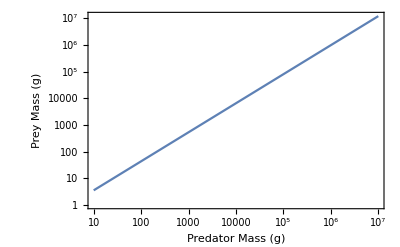

```mathematica
LogLogPlot[OptPreyMass[Mp],{Mp,10^1,10^7},Frame->True,FrameLabel->{"Predator Mass (g)","Prey Mass (g)"},LabelStyle->Directive[FontSize->16]]
```

```mathematica
(*OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;*)
(*Damuth: Average Individuals/m2*)
(*OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;*)
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[Mp_]:=YHerbperRes[OptPreyMass[Mp]];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; 
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify]; 
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
(*predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];*)
(*predatedconsumerdensity[Mp_,M_]:=1/Ypred[Mp,M];*)
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*1/Ypred[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];
b[Mp_] :=predmortalityfull[Mp,OptPreyMass[Mp]];

predgrowth =  FullSimplify[predgrowthrateperconsumer[Mp,M]]; (*predatedconsumerdensity without the 1/Yield*)
predgrowthfull[Mp_,M_]:=Evaluate[predgrowth//Simplify];
bPred[Mp_]:=predgrowthfull[Mp,OptPreyMass[Mp]];
(*bPred[M_]:=λPred[OptPredMass[M]];*)
(*bPredSub[M_]:=predgrowthfull[OptPredMass[M],M];*)
bPredSub[Mp_]:=Sub*λPred[Mp];



(*Predator starvation*)
σPred[M_]:=(1/τsig [OptPredMass[M]]);
kCons[M_]:=PreyDensityTheoreticalMax[M]; (*Consumer theroetical maximum*)
(*Predator mortality*) 
μPred[Mp_] := (a0*(Exp[a1*a2*Mp^(b1+b2)]-1)*Mp^(b0-b1-b2))/(a1*a2);   (* this is the consumer death rate*)
(*Subsidies could be set as mass dependent or mass-independent*)
(*Sub[M_]:=CsolNoSubsidies;*)
```

```mathematica
(*AverageCsolDensity=Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]];
Sub = ϵ*AverageCsolDensity;*)
Sub = ϵ*1;
```

```mathematica
Sub
```

ϵ

```mathematica
Esub = Integrate[(1/M)*Eprey[M],{M,1,10^7}]
```

459825.

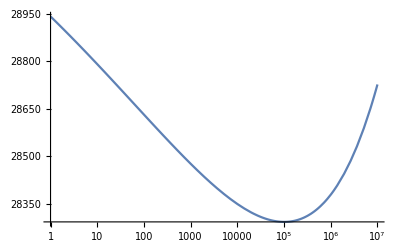

```mathematica
LogLinearPlot[Eprey[M],{M,1,10^7}]
```

```mathematica
Esub=Mean[Table[Eprey[M]/.M->10^i,{i,1,7,0.0001}]]
```

28472.1

```mathematica
(*Sub=Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]];*)(*1*)(*0.1*CsolNoSubsidies;*)
```

```mathematica
(*SubDensity=10*Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]]*)
```

Show the inputted PPMR

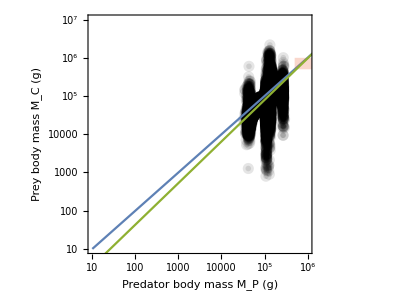

```mathematica
nlm = NonlinearModelFit[ExpPreymassdata*1000,nlm1*x^(nlm2),{nlm1,nlm2},x,MaxIterations->1000];
lm =LinearModelFit[Log@(ExpPreymassdata*1000),x,x];
lmparams=lm["BestFitParameters"];
nlmconfint=nlm["ParameterConfidenceIntervals",ConfidenceLevel->0.95];
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.1],FaceForm[Black],Disk[]}];
PPMRPlotNLM = Show[{
ListLogLogPlot[ExpPreymassdata*1000,Frame->True,FrameLabel->{"Predator body mass M_P (g)","Prey body mass M_C (g)"},LabelStyle->Directive[FontSize->16],ImageSize->500,AspectRatio->3/4,PlotMarkers->{pstyleherb,.010},PlotRange->{{10^1,1*10^6},{10^1,10^7}}],
ListLogLogPlot[Transpose[{Table[10^i,{i,1,7}],Table[10^i,{i,1,7}]}],Joined->True],
(*LogLogPlot[nlm[x],{x,100,5000}],*)
(*LogLogPlot[nlm[x],{x,100000,3200000},PlotStyle->Directive[Black,Thickness[0.008]]],
LogLogPlot[{nlmconfint[[1,1]]*x^(nlmconfint[[2,1]]),nlmconfint[[1,2]]*x^(nlmconfint[[2,2]])},{x,10^1,3200000},PlotStyle->Transparent,Filling->{1->{2}},FillingStyle->Directive[Green,Opacity[0.25]]],*)
(*ListLogLogPlot[predpreymassdata*1000,PlotStyle->Black],*)
(*LogLogPlot[Exp[lmparams[[1]]]*x^(lmparams[[2]]),{x,10^1,3200000},PlotStyle->ColorData[93,4]],*)
Graphics[{ColorData[97,4],Opacity[0.25],Rectangle[{Log@(5*10^5),Log@(5*10^5)},{Log@(2*10^7),Log@(1*10^6)}]}],
Graphics[Text[Style["Megatrophic range",FontSize->16,Black],{Log@(5*10^(5.5)),Log@(1*10^6)},Automatic]],
(*LogLogPlot[Exp[4]*Mp,{Mp,5,1.1*10^5},PlotStyle->ColorData[97,5]] (*Mathias general relationaship*),
LogLogPlot[Exp[3]*M,{M,5,1.1*10^5},PlotStyle->Directive[{ColorData[97,5],Dashed}]] (*Mathias felids relationaship*),*)
LogLogPlot[OptPreyMass[Mp],{Mp,10^1,10^7},Frame->True,FrameLabel->{"Prey Mass (g)","Predator Mass (g)"},LabelStyle->Directive[FontSize->16],PlotStyle->ColorData[97,3]]
},ImageSize->400,AspectRatio->3/4]
```

Calculate Intersection of Cruz/Pires relationship and Hayward relationship

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

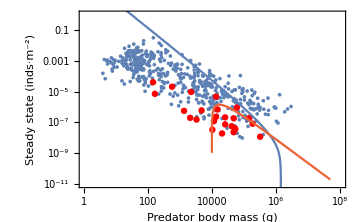

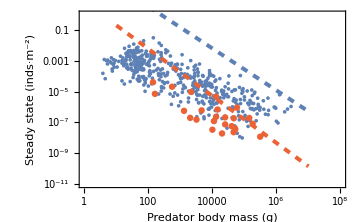

```mathematica
PercentGrowthConsumer=0.8; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidy =0.1;
PCDensityPlot=Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Predator body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidy},{Mp,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidy},{Mp,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Predator body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/OptPreyMass[Mp])*PreyDensityTheoreticalMax[OptPreyMass[Mp]]/.{w->PercentGrowthConsumer},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/Mp)*PredatorDensityTheoreticalMax[Mp,OptPreyMass[Mp]]/.{w->PercentGrowthConsumer},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_densities_PC.pdf"}],PCDensityPlot]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_densities_PC.pdf

MAYBE THIS ONE WORKS PRETTY GOOD NOT BAD MEH? 
****I THINK IT WORKS 3/24/23****

```mathematica
RealQ[x_]:=(Im[x]==0)===True; 
CsolMass = ((1/M)*Csol)/.M->Mass;
PsolMass = ((1/OptPredMass[M])*Psol)/.{M->Mass};
(*DJ=Det[JacobianFullModel];*)
DetectThresholdSol[DensitySol_,wvalue_,epsilonvalue_]:=
Module[{Sol = DensitySol},
maxexponent=8;
minexponent=1;
sollist =Table[{10^i,Sol/.{w->wvalue,Sub->epsilonvalue}/.Mass->10^i},{i,minexponent,maxexponent,0.05}];
sollistrealpos = Flatten[Position[sollist[[All,2]],_?(Re[#]>0 &&RealQ[#]&)],1];
sollistreal = sollist[[sollistrealpos]];
detminima = FindPeaks[-sollistreal[[All,2]]];
(*do any minima match the range limits?*)
massminima = sollistreal[[detminima[[All,1]],1]];
masslimitspos=Flatten[Position[massminima,_?(#==10^minexponent||#==10^maxexponent&)],1];
massminimarev=Drop[massminima,masslimitspos];
If[Length[sollistreal]==0,
exist = 0,
exist=1
];
If[Length[massminimarev]>0,
thresholdmass = massminimarev[[1]],
thresholdmass =Missing[]
];
{thresholdmass, exist}
];
```

```mathematica
{thresholdmass, exist}= DetectThresholdSol[PsolMass,0.5,0.001]
```

{11220.2,1}

```mathematica
wvalues = Table[i,{i,0.01,1,0.01}];
epsilonvalues = Table[10^i,{i,-3,0,0.005}];
CsolMass = ((1/OptPreyMass[Mp])*Csol)/.Mp->Mass;
PsolMass = ((1/Mp)*Psol)/.{Mp->Mass};
ThresholdsOverWEpsilonAlternate=Flatten[ParallelTable[
{thresholdsizeC,existC}= DetectThresholdSol[CsolMass,wvalues[[i]],epsilonvalues[[j]]];
{thresholdsizeP,existP} = DetectThresholdSol[PsolMass,wvalues[[i]],epsilonvalues[[j]]];
{wvalues[[i]],epsilonvalues[[j]],thresholdsizeC,thresholdsizeP, existC,existP},
{i,1,Length[wvalues]},{j,1,Length[epsilonvalues]}],1];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2Alternate_predpersp_large.csv"}],ThresholdsOverWEpsilonAlternate,"CSV"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon2Alternate_predpersp_large.csv

```mathematica
PreyThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],OptPreyMass[ThresholdsOverWEpsilonAlternate[[All,3]]]}];
(*PredThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],ThresholdsOverWEpsilonAlternate[[All,4]]}];*)
PredThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],ThresholdsOverWEpsilonAlternate[[All,4]]}];

PreySizeGapPosAlternate=Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#>4000&&#<20000&)],1];
PredSizeGapPosAlternate=Flatten[Position[PredThresholdMatrixAlternate[[All,3]],_?(#>4000&&#<20000&)],1];
PreyTMAlternate=PreyThresholdMatrixAlternate[[PreySizeGapPosAlternate,1;;2]];
PredTMAlternate=PredThresholdMatrixAlternate[[PredSizeGapPosAlternate,1;;2]];
MissingPosC = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#==Missing[]&)],1];
MissingPointsC = Transpose[{ThresholdsOverWEpsilonAlternate[[MissingPosC]][[All,1]],ThresholdsOverWEpsilonAlternate[[MissingPosC]][[All,2]]}];
MissingPosP = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,4]],_?(#==Missing[]&)],1];
MissingPointsP = Transpose[{ThresholdsOverWEpsilonAlternate[[MissingPosP]][[All,1]],ThresholdsOverWEpsilonAlternate[[MissingPosP]][[All,2]]}];

ExtinctPosC = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,5]],_?(#==0&)],1];
ExtinctPointsC = Transpose[{ThresholdsOverWEpsilonAlternate[[ExtinctPosC]][[All,1]],ThresholdsOverWEpsilonAlternate[[ExtinctPosC]][[All,2]]}];
ExtinctPosP = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,6]],_?(#==0&)],1];
ExtinctPointsP = Transpose[{ThresholdsOverWEpsilonAlternate[[ExtinctPosP]][[All,1]],ThresholdsOverWEpsilonAlternate[[ExtinctPosP]][[All,2]]}];
```

```mathematica
ThresholdPlotAlternate=GraphicsRow[{
Show[{
ListContourPlot[PreyThresholdMatrixAlternate,FrameLabel->{"% Growth from herbivore w","Subsidy density S (g·m^-2)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.01,1},All},ContourStyle->None,ColorFunction->"StarryNightColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"M_C^†",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PreyThresholdMatrix[[PreySizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PreyTMAlternate[[All,1]],Log@PreyTMAlternate[[All,2]]}]]}],
Graphics[{White,Opacity[1],ConcaveHullMesh[Transpose[{MissingPointsC[[All,1]],Log@MissingPointsC[[All,2]]}],0.02,All]}],
Graphics[{Gray,ConcaveHullMesh[Transpose[{ExtinctPointsC[[All,1]],Log@ExtinctPointsC[[All,2]]}],0.02,All]}]
}],
Show[{
ListContourPlot[PredThresholdMatrixAlternate,FrameLabel->{"% Growth from herbivore w","Subsidy density S (g·m^-2)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.001,1},All},ContourStyle->None,ColorFunction->"SiennaTones",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"M_P^†",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PredThresholdMatrix[[PredSizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PredTMAlternate[[All,1]],Log@PredTMAlternate[[All,2]]}]]}]
(*,
Graphics[{White,Opacity[1],ConcaveHullMesh[Transpose[{MissingPointsP[[All,1]],Log@MissingPointsP[[All,2]]}],0.02,All]}]*)
}]
},ImageSize->850,Spacings->0]
```

-Graphics-

```mathematica
Max[PreyThresholdMatrixAlternate[[All,3]]]
Min[PreyThresholdMatrixAlternate[[All,3]]]
```

Max[1.65097×10^6,667.475 Missing[]^0.426831]

Min[1873.3,667.475 Missing[]^0.426831]

```mathematica
(1*10^6)*63
```

63000000

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsoverwepsilon_predpersp_large.png"}],ThresholdPlotAlternate,"PNG"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsoverwepsilon_predpersp_large.png

```mathematica
PercentGrowthConsumer=1; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.08;
ConsDensityList=Table[{10^i,((1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.Mp->10^i},{i,1,8,0.01}];
ConsDensityListConsMass = Transpose[{OptPreyMass[ ConsDensityList[[All,1]]],ConsDensityList[[All,2]]}];
ThresholdPopulationPlotNoSub=
GraphicsRow[{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Predator body mass M_P (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^2.5),Log@(10^(-9))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
(*ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->ColorData[97,4]]*)
}],
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],*)
ListLogLogPlot[ConsDensityListConsMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^4.5),Log@(10^(-9))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
}]
},ImageSize->800];
PercentGrowthConsumer=0.5; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.08;
ConsDensityList=Table[{10^i,((1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.Mp->10^i},{i,1,8,0.01}];
ConsDensityListConsMass = Transpose[{OptPreyMass[ ConsDensityList[[All,1]]],ConsDensityList[[All,2]]}];
ThresholdPopulationPlotSub=
GraphicsRow[{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Predator body mass M_P (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^2.5),Log@(10^(-9))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
(*ListLogLogPlot[PredDensityListPredMass,Joined->True,PlotStyle->ColorData[97,4]]*)
}],
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer (M_C) Predator (M_P) body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],*)
ListLogLogPlot[ConsDensityListConsMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->20],{Log@(10^4.5),Log@(10^(-9))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
}]
},ImageSize->800];
ThresholdPopulationPlotComb=GraphicsColumn[{ThresholdPopulationPlotNoSub,ThresholdPopulationPlotSub},ImageSize->1000]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdspopcomb_predpersp.pdf"}],ThresholdPopulationPlotComb,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdspopcomb.pdf